# Data gen for Polynomial noise fit (non-Legendre)

## Data and Noise model

```mathematica
(* data model *)
dFunc[x_]:=0.5+1.5x;
(* x-dep precision β of normally distributed noise*)
varFunc[x_]:=10+5x+3.2 x^2;
(* stddev from precision, σ = 1/√β *)
sdFunc[x_]:=√varFunc[x];
```

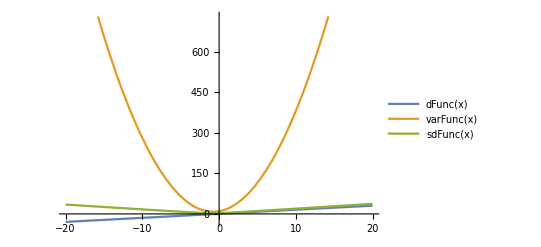

```mathematica
Plot[{dFunc[x], varFunc[x],sdFunc[x]},{x,-20,20},PlotLegends->"Expressions"]
```

## Data gen

```mathematica
dataPointsPerSet=200;
SeedRandom[1234];

xVals1 = RandomVariate[UniformDistribution[{-20,20}],dataPointsPerSet];
yVals1=dFunc@xVals1; 
noiseVals1=RandomVariate[NormalDistribution[0, sdFunc[#]]]&/@xVals1; 
tVals1=yVals1+ noiseVals1;
xtVals1 = Transpose@{xVals1,tVals1};
```

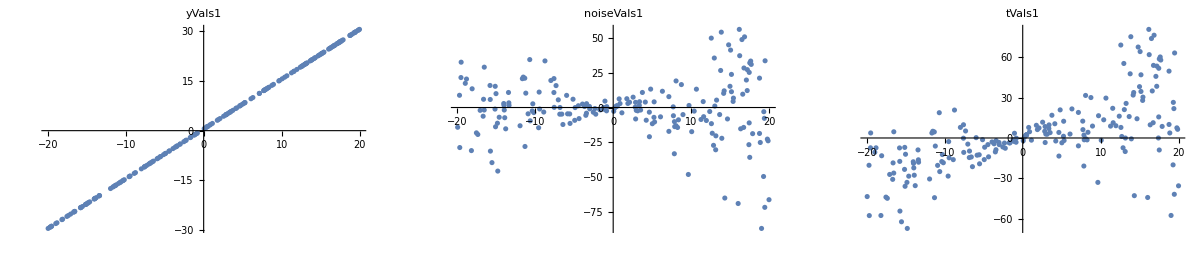

```mathematica
GraphicsRow[
{ListPlot[Transpose@{xVals1,yVals1},PlotLabel->"yVals1"],
ListPlot[Transpose@{xVals1,noiseVals1}, PlotLabel->"noiseVals1"],
ListPlot[xtVals1, PlotLabel->"tVals1"]},
ImageSize->Full
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["poly_xt_vals_200.csv",Transpose[xtVals1],"CSV"]
```

poly_xt_vals_200.csv